## Using PRIMAT. Fitting in Ω_b h^2, N_ν, τ_ν

### Loading PRIMAT

Setting the notebook directory (in batch mode this is not evaluated because it seems to be the default one)

```mathematica
SetDirectory[NotebookDirectory[]];
```

Then we go the parent directory, or base directory of PRIMAT.

```mathematica
SetDirectory[ParentDirectory[Directory[]]]
```

/Users/pitrou/Dropbox/iap/notebooks/BBN

We load PRIMAT. It takes some time because it starts reading the file with nuclear reactions and deduces which are the nuclides needed, 
and it starts to build formally the network of equations

```mathematica
Timing[<<PRIMAT-Main.m]
```

{16.0244,Null}

### Set up

Just to be sure we reset all parameters

```mathematica
$DegenerateNeutrinos=False;
$RandomNuclearRates=False;
$Randomh2Ωb=False;
$Randomτneutron=False;

Meanh2Ωb0=h2Ωb0;
Meanτneutron=τneutron;
μOverTν=0;
ϕold=μOverTν;
NeutrinosGenerations=3;
```

Table used for interpolationin Ω_b h^2 , N_ν , τ_n

```mathematica
TableωNτ=Table[{ω,Νν,τn},{ω,Meanh2Ωb0*0.90,Meanh2Ωb0 *1.10,Meanh2Ωb0*0.10/16},{Νν,2,4,1/16},{τn,Meanτneutron*0.98,Meanτneutron*1.02,Meanτneutron*0.02/2}];
```

We define a parallelization to make it faster

```mathematica
$ParallelBoolFit=True;
If[$ParallelBoolFit,InitializeKernels;
ParallelEvaluate[$HistoryLength=0;]];
MyMap:=If[$ParallelBoolFit,ParallelMap,Map]
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

Number of Kernels 2

This function compute the abundances for a given set of {ω, Nν, τn} parameters. 
We do not use Monte-Carlo on rates and we have set accordingly all Random Booleans to False above.

```mathematica
ComputePrincipalAbundanceωNτNOMC[{ω_,Nν_,τn_}]:=Module[{ResultMean,Resultσ,Meanh2Ωb0Old,MeanτneutronOld,NeutrinosGenerationsOld},
NeutrinosGenerationsOld=NeutrinosGenerations;
Meanh2Ωb0Old=Meanh2Ωb0;
MeanτneutronOld=Meanτneutron;
NeutrinosGenerations=Nν;
Meanh2Ωb0=ω;
Meanτneutron=τn;


Print["Running Kernel ",$KernelID," ",Meanh2Ωb0," ",NeutrinosGenerations," ",Meanτneutron];
$ParallelBool=False;
RunPRIMAT;

YP=4ElementColumn["a"];
YDH=10^5 ElementColumn["d"]/ElementColumn["p"];
YHe3H=10^5(ElementColumn["t"]+ElementColumn["He3"])/ElementColumn["p"];
YLi7H=10^10(ElementColumn["Li7"]+ElementColumn["Be7"])/ElementColumn["p"];

NeutrinosGenerations=NeutrinosGenerationsOld;
Meanh2Ωb0=Meanh2Ωb0Old;
Meanτneutron=MeanτneutronOld;
{YP,YDH,YHe3H,YLi7H}
]
```

We launch it it takes hours

```mathematica
MachineNumerics=""(*$MachineName*);

Timing[TableYsLowMiddleUp6=MyMap[ComputePrincipalAbundanceωNτNOMC,TableωNτ,{3}];];
Export["MonteCarlo/YsOmegaNuTauNOMC"<>MachineNumerics<>".mx",TableYsLowMiddleUp6,"MX"];
```

Running Kernel 2 0.020025 2 861.714

Running Kernel 1 0.0208594 2 861.714

$Aborted

### Analysis

```mathematica
MachineOfRuns="";
```

```mathematica
TableYsLowMiddleUp6=Import["MonteCarlo/YsOmegaNuTauNOMC"<>MachineOfRuns<>".mx"];
Meanh2Ωb0=h2Ωb0;
Meanτneutron=τneutron;
```

```mathematica
TableYsLowMiddleUp6//Dimensions
```

{33,33,5,4,1}

Interpolations

```mathematica
Clear[YωNτ,gDH,gYP,gHe3,gLi7]
gYP[{ω_,N_,τ_},L_List]:={ω,N,τ,Mean[L[[1]]]};
gDH[{ω_,N_,τ_},L_List]:={ω,N,τ,Mean[L[[2]]]};
gHe3[{ω_,N_,τ_},L_List]:={ω,N,τ,Mean[L[[3]]]};
gLi7[{ω_,N_,τ_},L_List]:={ω,N,τ,Mean[L[[4]]]};

YωNτ[Type_String]:=YωNτ[Type]=Switch[Type,
"YP", Interpolation[Flatten[MapThread[gYP,{TableωNτ,TableYsLowMiddleUp6},3],2]],
"DH", Interpolation[Flatten[MapThread[gDH,{TableωNτ,TableYsLowMiddleUp6},3],2]],
"He3", Interpolation[Flatten[MapThread[gHe3,{TableωNτ,TableYsLowMiddleUp6},3],2]],
"Li7", Interpolation[Flatten[MapThread[gLi7,{TableωNτ,TableYsLowMiddleUp6},3],2]]
]
```

Fitting polynomials

```mathematica
RefY[Type_]:=YωNτ[Type][Meanh2Ωb0,3,Meanτneutron]
```

```mathematica
RefY["YP"]
RefY["DH"]
```

0.247093

2.45919

```mathematica
Clear[TabPost,TabPostDH,TableFit,fitY]
TableFit=TableωNτ(*Flatten[Table[{ω,Nν},{ω,Meanh2Ωb0*0.95,Meanh2Ωb0*1.05,Meanh2Ωb0*0.001},{Nν,2.5,3.5,0.01}],1]*);

TabPost[Type_String]:=TabPost[Type]={Sequence@@#,(YωNτ[Type]@@#-RefY[Type])/RefY[Type]}&/@(Flatten[TableFit,2]);
```

```mathematica
ModelPost=(a100 (ω-Meanh2Ωb0)/Meanh2Ωb0+ a010 (Nν-3)/3 + a110(ω-Meanh2Ωb0) /Meanh2Ωb0(Nν-3)/3+a200 (ω-Meanh2Ωb0)^2/Meanh2Ωb0^2+a020 (Nν-3)^2/3^2+a300 (ω-Meanh2Ωb0)^3/Meanh2Ωb0^3+a210 (ω-Meanh2Ωb0)^2/Meanh2Ωb0^2((Nν-3)/3)+a120 (ω-Meanh2Ωb0)^1/Meanh2Ωb0^1((Nν-3)/3)^2+a030 ((Nν-3)/3)^3)+(τn-Meanτneutron)/Meanτneutron*(a001 +a101 (ω-Meanh2Ωb0)/Meanh2Ωb0+ a011 (Nν-3)/3 + a111(ω-Meanh2Ωb0) /Meanh2Ωb0(Nν-3)/3+a201 (ω-Meanh2Ωb0)^2/Meanh2Ωb0^2+a021 (Nν-3)^2/3^2(*+a301 (ω-Meanh2Ωb0)^3/Meanh2Ωb0^3+a211 (ω-Meanh2Ωb0)^2/Meanh2Ωb0^2((Nν-3)/3)+a121 (ω-Meanh2Ωb0)^1/Meanh2Ωb0^1((Nν-3)/3)^2+a031((Nν-3)/3)^3*));
```

```mathematica
Clear[fitY]
fitY[Type_String]:=fitY[Type]=FindFit[TabPost[Type],ModelPost,{a100,a010,a110,a200,a020,a300,a210,a120,a030,a001,a101,a011,a111,a201,a021(*,a301,a211,a121,a031*)},{ω,Nν,τn}]
```

The actual constants of the fits

```mathematica
fitY["YP"]//TableForm
fitY["DH"]//TableForm
fitY["He3"]//TableForm
fitY["Li7"]//TableForm
```

a100→0.0390391
a010→0.163552
a110→-0.0000440413
a200→-0.0293506
a020→-0.0361242
a300→0.0178913
a210→-0.00103698
a120→-0.000354166
a030→0.0099378
a001→0.731614
a101→-0.00974149
a011→0.0183209
a111→-0.00342291
a201→0.00418929
a021→-0.0119812

a100→-1.6455
a010→0.409007
a110→-0.612292
a200→2.04137
a020→-0.00598844
a300→-2.40817
a210→0.801501
a120→-0.00477233
a030→0.00224146
a001→0.4222
a101→-0.660303
a011→0.193671
a111→-0.331577
a201→0.906169
a021→0.00497784

a100→-0.566992
a010→0.135868
a110→-0.12157
a200→0.53303
a020→-0.0126467
a300→-0.518549
a210→0.120829
a120→0.00928494
a030→0.00270194
a001→0.140525
a101→-0.123898
a011→0.0404025
a111→-0.0387862
a201→0.121213
a021→-0.00328164

a100→2.07605
a010→-0.276754
a110→-0.292767
a200→0.586393
a020→0.038878
a300→-0.882435
a210→0.510822
a120→-0.103354
a030→0.0088363
a001→0.438295
a101→1.22619
a011→-0.330694
a111→-0.709229
a201→0.92463
a021→0.135303

Maximum relative error evaluation

```mathematica
Max[Apply[Function[{ω,Nν,τn},Evaluate[Abs[RefY[#](1+ModelPost/.fitY[#])/YωNτ[#][ω,Nν,τn]-1]]],Flatten[TableFit,2],1]]&/@{"YP","DH","He3","Li7"}
```

{0.000136916,0.000350117,0.0000357168,0.000279726}

We plot the reconstructions

```mathematica
Clear[fType]
fType[Type_][ω_,Nν_,τn_]={ω,Nν,τn,ModelPost/.fitY[Type]};
```

ReplaceAll::reps: {fitY[Type]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Clear[ReplaceListFit]
ReplaceListFit[Type_String]:=ReplaceListFit[Type]=Apply[fType[Type],Flatten[TableFit,2],1]
```

```mathematica
ReplaceListFit["YP"];
```

```mathematica
Clear[Rebuild]
Rebuild[Type_String]:=Rebuild[Type]=Interpolation[ReplaceListFit[Type]];
```

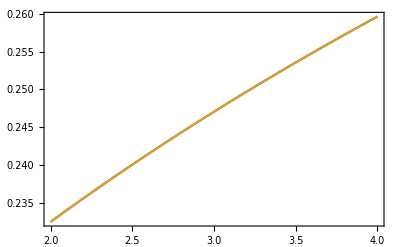

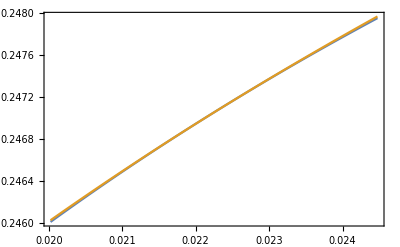

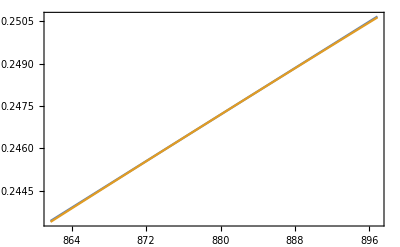

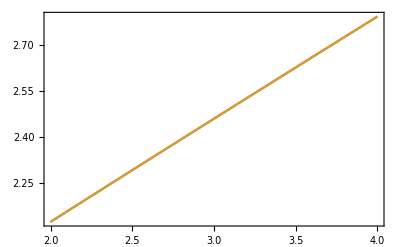

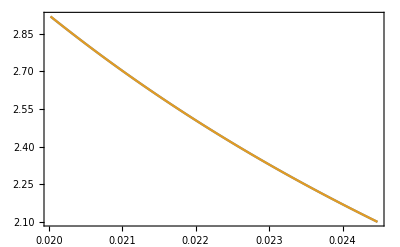

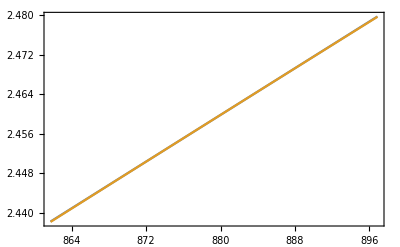

```mathematica
Plot[{RefY["YP"](1+Rebuild["YP"][Meanh2Ωb0,Nν,Meanτneutron]),YωNτ["YP"][Meanh2Ωb0,Nν,Meanτneutron]},{Nν,2.,4},Frame->True]
Plot[{RefY["YP"](1+Rebuild["YP"][ω,3.,Meanτneutron]),YωNτ["YP"][ω,3.,Meanτneutron]},{ω,Meanh2Ωb0*0.9,Meanh2Ωb0*1.1},Frame->True]
Plot[{RefY["YP"](1+Rebuild["YP"][Meanh2Ωb0,3.,τ]),YωNτ["YP"][Meanh2Ωb0,3.,τ]},{τ,Meanτneutron*0.98,Meanτneutron*1.02},Frame->True]

Plot[{RefY["DH"](1+Rebuild["DH"][Meanh2Ωb0,Nν,Meanτneutron]),YωNτ["DH"][Meanh2Ωb0,Nν,Meanτneutron]},{Nν,2.,4},Frame->True]
Plot[{RefY["DH"](1+Rebuild["DH"][ω,3.,Meanτneutron]),YωNτ["DH"][ω,3.,Meanτneutron]},{ω,Meanh2Ωb0*0.9,Meanh2Ωb0*1.1},Frame->True]
Plot[{RefY["DH"](1+Rebuild["DH"][Meanh2Ωb0,3.,τ]),YωNτ["DH"][Meanh2Ωb0,3.,τ]},{τ,Meanτneutron*0.98,Meanτneutron*1.02},Frame->True]
```